```mathematica
?Graphics
```

```mathematica
?Rectangle
```

Rectangle[{x_min,y_min},{x_max,y_max}] represents an axis-aligned filled rectangle from {x_min,y_min} to {x_max,y_max}.
Rectangle[{x_min,y_min}] corresponds to a unit square with its bottom-left corner at {x_min,y_min}.

```mathematica
Graphics[{
{Pink,EdgeForm[{Thick,Black}],Disk[{0,10},1]},
{Yellow,EdgeForm[{Thick,Black}],Triangle[{{0,9},{-3,6},{3,6}}]},
{Pink, EdgeForm[{Thick, Black}],Rectangle[{1,5.5},{1.2,7.3}]},
{Pink, EdgeForm[{Thick, Black}],Rectangle[{-1,7.3},{-1.2,9.3}]},
{Pink, EdgeForm[{Thick, Black}],Rectangle[{1,5.5},{1.2,7.3}]},
{Pink, EdgeForm[{Thick, Black}],Rectangle[{0.5,3},{0.9,6}]},
{Pink, EdgeForm[{Thick, Black}],Rectangle[{-0.5,3},{-0.9,6}]}
}]
```

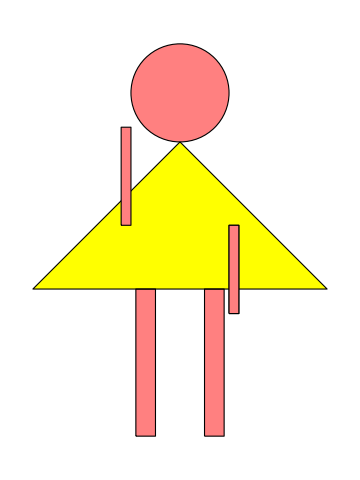

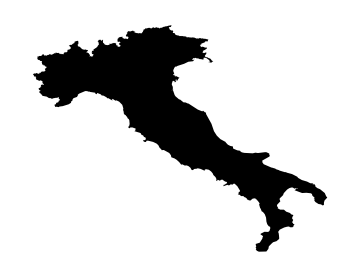

```mathematica
Italy= Import[NotebookDirectory[]<> "ItalyBorder.dat"];
Graphics[
Polygon[Italy],ImageSize->Medium
]
```

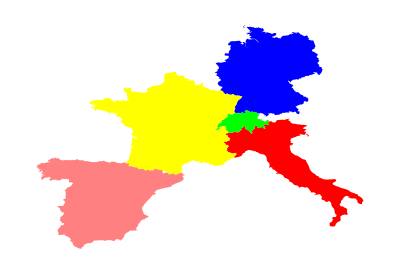

```mathematica
italy=Import[NotebookDirectory[]<>"ItalyBorder.dat"];
germany=Import[NotebookDirectory[]<>"GermanyBorder.dat"];
spain=Import[NotebookDirectory[]<>"SpainBorder.dat"];
france=Import[NotebookDirectory[]<>"FranceBorder.dat"];
switzerland=Import[NotebookDirectory[]<>"SwitzerlandBorder.dat"];

Graphics[{
{Red,Polygon[italy],ImageSize->Medium},
{Blue,Polygon[germany],ImageSize->Medium},
{Pink,Polygon[spain],ImageSize->Medium},
{Yellow,Polygon[france],ImageSize->Medium},
{Green,Polygon[switzerland],ImageSize->Medium}
}]
```